## DivideEdge-Example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Warning: Cellzilla2D: xSSA.m not found in path. Some stochastic conversion functions may not work as expected. It should be loaded manually before any xSSA (stochastic) simulations can be run.

Cellzilla2D (3.0.51 (05 June 2017)) loaded Wed 7 Jun 2017 12:45:32
using xCellerator 0.95 and XSSA ** Not Found **
GPL License Terms Apply

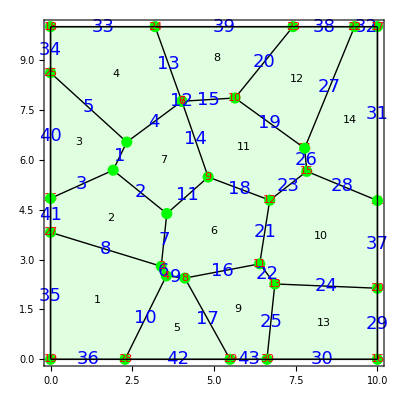

```mathematica
w=TemplateRandomSquareGrid[12, {0,0}, {10,10}];
ShowTissue[w,  "Vertices"-> {Green,PointSize[.02]},"VertexNumbers"-> {Red, FontSize-> 18}, "EdgeNumbers"->True, "EdgeNumberStyle"->  {Blue, FontSize-> 18, FontFamily-> "Arial"}, "CellNumbers"-> True, Frame-> True]
```

## Evenly divide up a single edge

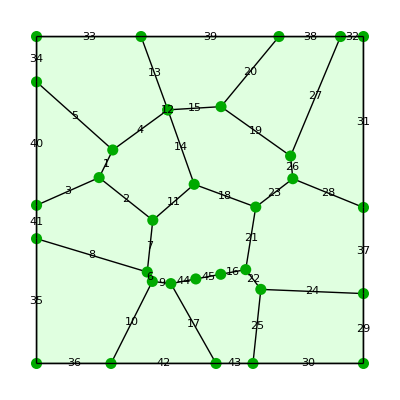

```mathematica
w1=DivideEdge[w, 16, 3];
ShowTissue[w1, "Vertices"-> {Darker[Green], PointSize[.02]}, "EdgeNumbers"-> True]
```

## Divide sequence of edges evenly into sub-edges

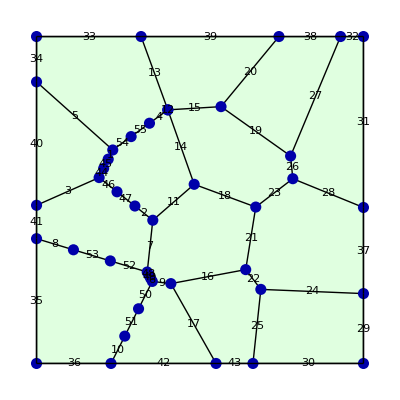

```mathematica
w2=DivideEdges[w, {1,2,6,10,8,4}, 3]; 
ShowTissue[w2, "Vertices"-> {Darker[Blue], PointSize[.02]}, "EdgeNumbers"-> True]
```

## Divide single edge at an explicit coordinate location

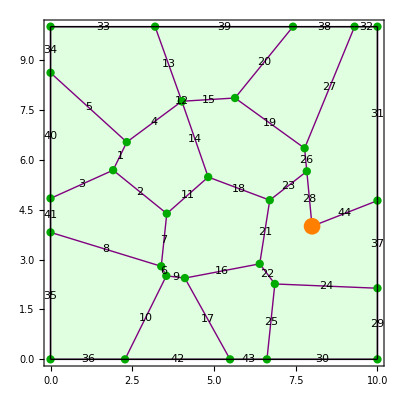

```mathematica
w3=DivideEdge[w, 28, {8,4}]; 
ShowTissue[w3, "Vertices"-> {Darker[Green], PointSize[.015]}, "EdgeStyles"-> {Purple}, "EdgeNumbers"-> True, Epilog-> {Orange,PointSize[.03],  Point[{8,4}]},Frame-> True]
```